# Elemental analysis of the Spanish Government Twitter Account in 2020 with Mathematica Software (Part I)

## Jesús Martín Ovejero.

## Abstract: In the last ten years, programming languages as Python or R, have been established as indispensable tools in the armory of every Data Scientist, but, the new features of Wolfram Mathematica together with the fast development of other Wolfram Technologies allow us to suggest that Python and R hegemony is nearing its end. In the present notebook, we do an elemental analysis of the Spanish Government Twitter account using the software Mathematica. This short essay aims to show the potential use of Wolfram Technologies to analyze and manipulate data. This is the first part of a series of notebooks to show the versatility of Wolfram Language to analyze data and its potential use in finance analysis.

This notebook will be focused on the following points:

1) Extract information of a user Twitter account and bypass the rate limit of the API. 

2) Use basic visualization tools to explore the data we have obtained. 

3) Clean the data and perform a sentimental analysis.

To download the notebook go to:  https://github.com/JMartinOvejero/Data-Analysis-with-Wolfram-Mathematica

I would like to thank Wolfram U for the opportunity to learn from so many experts in the field.


In the first place,  to collect the tweets of the Spanish Government, we should connect with Twitter. There is a built-in API that allow us to access to Twitter:

```mathematica
twitter=ServiceConnect["Twitter",SaveConnection->True]
```

ServiceObject[…]

The Spanish Government nickname at Twitter is @desdelamoncloa. Let us download the last 3222 tweets (rate limiting of Twitter API) posted by the Spanish Government Twitter account and let us store them in a variable called SpainTweets:

```mathematica
SpainTweets=twitter["TweetList","Username"->"desdelamoncloa","MaxItems"->5000,"Elements"->"FullData"];
```

```mathematica
Dimensions[SpainTweets]
```

{3222,11}

To see the attributes of the data we have collected, let us consider a random Tweet:

```mathematica
RandomSample[SpainTweets,1];
%[[1]]
```

Dataset[<>]

With two lines of code, and using the internal architecture of Mathematica, we can visualize the number of tweets posted on each day of the week and also at what time were posted them:

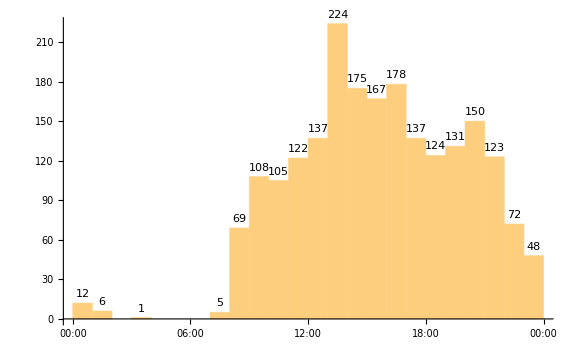

```mathematica
DateHistogram[SpainTweets[All,"Date"],"Hour", 
											DateReduction->"Day", LabelingFunction->Above, ImageSize->Large]
```

Let us obtain the most popular tweets posted by @desdelamoncloa,  i.e the Tweets with higher Favorite count  and Retweet count.

```mathematica
RetCount=Floor[SpainTweets[Max,"RetweetCount"]]
```

11750

```mathematica
FavCount=Floor[SpainTweets[Max,"FavoriteCount"]]
```

2497

```mathematica
SpainTweets[
			Select[ 
					#RetweetCount≥RetCount||
					#FavoriteCount≥FavCount &],
{"Text","Hashtags","FavoriteCount","RetweetCount"}]
```

Dataset[<>]

To perform an analysis of the Hashtags used by the Twitter account, we can sort the Hashtags by the number of times they were posted:

```mathematica
SpainHashtags=SpainTweets[Flatten/*Counts/* ReverseSort, "Hashtags"]
```

Dataset[<>]

To visualize the frequency of the Hashtags  we can use a word cloud:

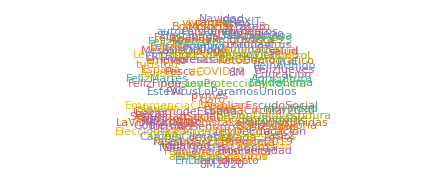

```mathematica
SpainTweets[Flatten/*WordCloud,"Hashtags"]
```

Using the same techniques, we can create a word cloud out of the text content in the tweets in order to infer the main topics discussed in the tweets. Before doing this operation we must clean our data. With this aim, we remove undesired words and characters by defining a function called CleanText. In order to construct CleanText we must define a function to remove stopwords in Spanish.

```mathematica
stopwords={" un ", " una ", " uno ", " unos ", " unas ", " nosotros ", " nosotras ", " vosotros ", " vosotras ", " el "," El ",  " la ", " La ", " han ", " lo ", " los ", " que " , " y ", " a ", " ante ", " bajo ", " con ", " contra" , " de ", " desde ", " en ", " entre ", " hacia ", " hasta ", " para ", " Para ", " Este ", " Esta ", " La " , " las ", " se" ,  " por ", " según ", " sobre ", " tras ", " también ", " por ", " ser ", " somos ", " esta ", " está ", " estamos ", " somos ", " estais ", " hacer ", " haciendo " , " otro ", " algún ",  " porque ", " por qué ", " sin ", " usar ",  " ciertos ", " cierto ", " todo ", " todos ", " todas ", " del " , " al ", " No ", " Si "; " más ", " ha ", " son " };

CleanText[text_String]:=StringDelete[StringDelete[text,stopwords],{Except[{"@","#","_"},PunctuationCharacter],"http"~~Except[WhitespaceCharacter]}]
```

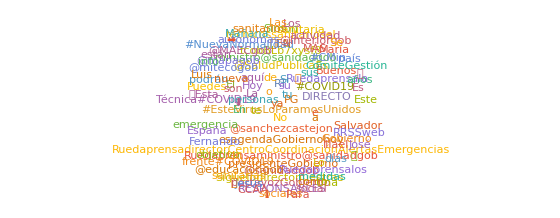

```mathematica
SpainTweets[All/* StringSplit /* WordCloud, "Text", CleanText]
```

We can get a list of the mentioned  users, but before this, we must write a function to extract user mentions and add them back to the structured data:

```mathematica
getUserMentions[tweet_Association]:=Module[{modifiedTweet=tweet},AssociateTo[modifiedTweet,"Usermentions"->Flatten[StringCases[tweet["Text"],"@"~~u:(LetterCharacter|DigitCharacter|"_")..~~(WhitespaceCharacter|PunctuationCharacter|EndOfString):>u]]]];
```

```mathematica
SpainTweets=Dataset[getUserMentions/@ Normal @SpainTweets];
```

```mathematica
MentionUsers=Normal[SpainTweets[Flatten/*DeleteDuplicates,"Usermentions"]]
```

{policia,guardiacivil,glblctzn,sanchezcastejon,Congreso_Es,GAFSPfund,GlblCtzn,VSocialGob,INCIBE,mitecogob,MAECgob,mapagob,sanidadgob,Haciendagob,_minecogob,ICOgob,Defensagob,paradores,empleogob,inclusiongob,Yolanda_Diaz_,joseluisescriva,Senadoesp,gavi,UniversidadGob,salvadorilla,NadiaCalvino,ComisionEuropea,boegob,UE_Comision,educaciongob,territorialgob,Alimentacion_es,sanidad,igualdad,CasaReal,interiorgob,oapngob,mincoturgob,justiciagob,EU_Comm,CooperacionESP,proteccioncivil,SaludPublicaEs,Enisa,mitmagob,consumogob,Teresaribera,Adif_es,Renfe,redpuntoes,DelGobVG,CienciaGob,maec,culturagob,CSIC,deportegob,haciendagob,vsocialgob,SaludISCIII,spain,DGTes,salvamentogob,jmrdezuribes,museodelprado,comisionadoPI,EU_Commission,museoreinasofia,MuseoThyssen,empleo_SEPE,CDTIoficial,CruzRojaEsp,_CARITAS,Cermi_Estatal,AEMPSGOB,UN,OECD,rtve,Congreso,WHO,Sanidadgob,Dragonsaulo,CineICAA,LuisPlanas,IgualdadGob,alertcops,CEOE_ES,cepyme_,UGT_Comunica,CCOO,SE_Comercio,camarascomercio,Aebanca,sec,TwitterEspana,CREASGR,EUCouncil,IGNSpain,CNB_CSIC,osiseguridad,dsn,es_INE,MarotoReyes,Faconauto_com,fempcomunica,platdeinfancia,SEDIAgob,ECDC_EU,Vinxco,javidearnedo,josemdomenech2,astefanov5,s,Ineco_es,NormasUNE,SaludISCII,Sani,SanidadGob,AndaluciaJu,hans_kluge,WHO_Europe,aena,cienciagob,AlertCops,desdelamoncloa,idae,ve,AranchaGlezLaya,micoturgob,la2_tve,Clan_tve,UMEgob,060gobes,SaludMadrid,EjercitoTierra,feriademadrid,CrueUniversidad,boe,mscbs,EjercitoTierr,M_Presidencia,defensagob,EmbEspanaRabat,astro_duque,GiuseppeConteIT,autonomosata,ilo,EspanaGlobal,jensspahn,olivierveran,Fridays4future,HablamosdEuropa,joaquinaraujo,AnfacAutomovil,AEMET_Esp,OITnoticias,ThierryBreton,lariojaorg,ConchaAndreu,sanidadgo,abalosmeco,Co,mjmonteroc,realessitios,InjuveSpain,112canarias,ENAIRE,GranCanariaCab,CabildoTenerife,PlanTIFIES,AgEInves,Inmujer,Oceanicas_IEO,AnimalesGob,Armada_esp,EjercitoAire,congreso_Es,Agenda2030Gob,opengovpart,IDAEenergia,usal,iaa_csic,imb_cnm,ONU_es,MWCapital,EmbSpainUK,UNESCO,FCBfemeni,MSCActions,CarolinaDarias,CelaaIsabel,carmencalvo_,antoniobanderas,Red_Carolina,Turespana_,nuria,diba,nuriamarinlh,FomentTreball,eucopresident,CarrefourES,112cmadrid,sepiegob,EUErasmusPlus,AEPD_es,Twitter,SpainWpFem,SpainWP,marcoaguiriano,Agenda2030Esp,EmbEspChina,maecgob,Europarl_ES,FBiodiversidad,astro_d,es,RFEBalonmano,san,is4k,JLambanM,TheEconomist,wef_es,fitur_madrid,La1_tve,24h_tve,rne,educaINTEF,CMNUCC,InfoAdif,GVA112,112Aragon,redrunacional,CEAPA3,PNSDgob,AECID_es,proyectoMusaE,educaINEE,IRENA,ATPCup,Permafrost_UAH,UNFCCC,fomentogob,el_pais,EU_Careers,Inforenfe,PuertosEstado,museothyssen,ESA_CHEOPS,esa,Refugees,FECYT_Ciencia,jcyl,DGCyL,ipcepatrimonio}

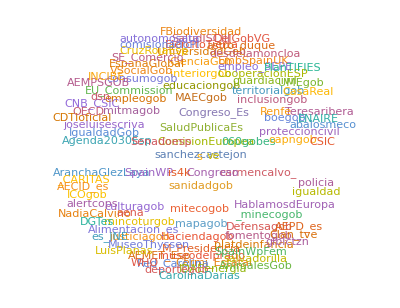

```mathematica
SpainTweets[Flatten/*WordCloud, "Usermentions"]
```

Due to the rate limits on the number of calls to the Twitter API we can not download the users data directly. For this reason we have to bypass the API:

```mathematica
numRequests=180;
intervals=Ceiling[Length[MentionUsers]/numRequests]
```

2

getTwitterData is a function that allow us to donwload UserData from Twitter, given a list of userNames from the mentionedUser list:

```mathematica
getTwitterData[request_String,userNames_List]:=twitter[request,"Username"->#]&/@userNames;
```

Setting up a scheduled task to download user data across multiple rate-limited windows:

```mathematica
i=1;
data={};
SessionSubmit[
	ScheduledTask[
			AppendTo[data,getTwitterData["UserData",Partition[MentionUsers,UpTo[numRequests]][[i++]]]],
							{Quantity[15,"Minutes"],intervals}],
							HandlerFunctions-><|"TaskStatusChanged"->(Print["Task status: ",#TaskStatus]&)|>,HandlerFunctionsKeys->{"TaskStatus"}]
```

Task status: Running

```mathematica
TaskObject[<|TaskUUID -> 197b2c8e-5131-46d6-bcdc-5a8f7a66e060, TaskEnvironment -> Session, TaskType -> Scheduled, EvaluationExpression :> AppendTo[data, getTwitterData[UserData, Partition[MentionUsers, UpTo[numRequests]][[i++]]]], Schedule -> <|Type -> Repeated, TotalRunCount -> 2, <<2>>, EndDate -> Infinity|>, <<1>>, HandlerFunctionsKeys -> {TaskStatus}, AutoRemove -> True|>]
```

```mathematica
MentionedUserData=data;
CleanMentionedUserData=Dataset[DeleteCases[Flatten[MentionedUserData],Except[_Association]]];
```

```mathematica
RandomSample[CleanMentionedUserData]
```

Dataset[<>]

We can also visualize the location of each mentioned user with the function GeoListPlot

```mathematica
locations=Interpreter["ComputedLocation"]/@Normal@CleanMentionedUserData[All,"Location"];
```

```mathematica
GeoListPlot[DeleteCases[locations,Except[GeoPosition[{_,_}]]]]
```

-Graphics-

We can use the built-in function “Sentiment” to classify the sentimentes of the tweets posted by @desdelamoncloa.  This classifier catalogue each tweet as Positive, Negative, Neutral or Indeterminate.

```mathematica
labels=Classify["Sentiment",SpainTweets[All,"Text",CleanText]];
labels[[1;;10]]
```

{Positive,Positive,Positive,Positive,Positive,Positive,Positive,Neutral,Positive,Positive}

```mathematica
PieChart[Counts[labels],ChartLabels->Placed[Automatic,"RadialOuter"]]
```

-Graphics-

As we can see, “Negative” and “Indeterminate” tweets are unlikely, so let us check their contents:

```mathematica
Cases[({#1->Classify["Sentiment",CleanText[#1]]}&)/@SpainTweets[All,"Text"],{_->"Negative"}]
```

Dataset[<>]